# QCD phase transitions for NNaturalness - Tests 01

```mathematica
ClearAll["Global`*"]
```

## NNaturalness parameters

Masses in GeV

```mathematica
mh0 = 88 (*Our Higgs mass, GeV*)
quadCutOff[N_,r_] = mh0*Sqrt[N/r]
```

88

88 √(N/r)

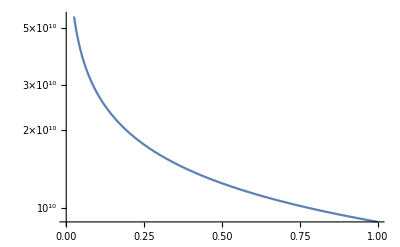

```mathematica
LogPlot[quadCutOff[10^16,r],{r,0,1}]
```

```mathematica
mHi[N_,r_,i_]= quadCutOff[N,r]*Sqrt[(-2i-r)/N](*i negative in this case - independent of N, just in so it has the same form as from the paper*)
```

88 √((-2 i-r)/N) √(N/r)

```mathematica
mH1 =mHi[10^8,1,-1]
```

88

## Critical values of i

Assuming that, at high scales, the strong coupling is identical between sectors (so, at high scales Λ_QCD = Λ_IQCD = 90.6 MeV (PDG)), we can run down the coupling and determine which sector i strong first-order phase transitions begin. Here, k is a slop factor that can be adjusted to take into account how close to Λ_QCD the up quark mass needs to be for the PT to become strongly 1st order.

```mathematica
CritIndex[mu_,ms_,mc_,mb_,mt_,qcd_,k_] = ((ms*mc*mb*mt)^(4/25))(qcd^(42/25))/(k*mu)^(58/25)
```

((mb mc ms mt)^(4/25) qcd^(42/25))/(k mu)^(58/25)

```mathematica
CritIndex[2.3,95,1275,4180,173000,91,0.2]
CritIndex[2.3,95,1275,4180,173000,91,1]
CritIndex[2.3,95,1275,4180,173000,91,10]
```

2.01551×10^6

48169.7

230.555

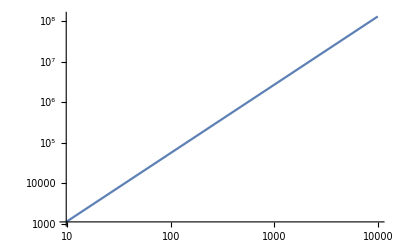

```mathematica
LogLogPlot[CritIndex[2.3,95,1275,4180,173000,x,1],{x,0,10000}]
```

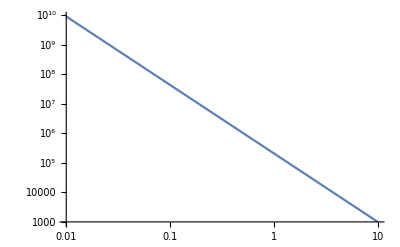

```mathematica
LogLogPlot[CritIndex[2.3,95,1275,4180,173000,218,x],{x,0.01,10}]
```

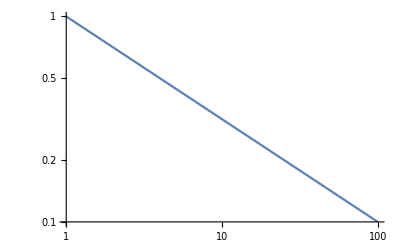

```mathematica
LogLogPlot[i^(-1/2),{i,1,100}]
```

```mathematica
N[Sum[i^(-2)*10^(-2), {i,1,1000}]]
```

0.0164393

```mathematica
N[%]
```

0.0164393

## Exotic Quark and Pion Masses

From NNaturalness, page 2 and Spontaneous Mirror Parity Violation, Common Origin ofMatter and Dark Matter, and the LHC Signatures. Inputs in MeV, outputs in eV

```mathematica
ΛEQCD =N[ 218^(23/21)/(173000)^(2/21)]
```

115.426

```mathematica
FermionEMass[mHei_,LambdaQCD_,smQM_]:= (smQM/246000)(173000/246000)(LambdaQCD^3/mHei^2)
```

```mathematica
ueMass =FermionEMass[88000,91,2.3]*10^6
deMass =FermionEMass[88000,91,4.8]*10^6
seMass=N[FermionEMass[88000,91,95]]*10^6
ceMass=N[FermionEMass[88000,91,1290]]*10^6
beMass=N[FermionEMass[88000,91,4180]]*10^6
teMass=N[FermionEMass[88000,91,173000]]*10^6
```

0.000639827

0.00133529

0.0264276

0.358859

1.16282

48.1261

Here the pion mass is calculated by using a ratio of Gell-Mann-Oakes-Renner relations, see Schwarts 28.2.2 for details. The pion mass is approximated at 135 MeV

```mathematica
pioneMass = Sqrt[(ueMass + deMass)/((2.3+4.8)*10^6)]*(135000000)
```

2251.65

```mathematica
medpioneMass = Sqrt[(ceMass+beMass)/((2.3+4.8)*10^6)]*(135000000)
bigpioneMass = Sqrt[(teMass+deMass)/((2.3+4.8)*10^6)]*(135000000)
bigerpioneMass = Sqrt[(teMass+seMass)/((2.3+4.8)*10^6)]*(135000000)
biggestpioneMass = Sqrt[(teMass+beMass)/((2.3+4.8)*10^6)]*(135000000)
```

62497.9

351480.

351572.

355696.

These calcs are done for the first exotic sector (temperatures taken from GW calc doc 2). Units are GeV

```mathematica
TnucE =0.218;
TPTUs=3.65952;
ρR = 271304;
alphaInf = TnucE^2/(ρR*TPTUs)(medpioneMass^2 +bigpioneMass^2 + bigerpioneMass^2 + biggestpioneMass^2)/(24*10^(18))(*The final term is to convert the pion masses to GeV*)
```

7.53036×10^-16

## Degrees of Freedom

#### Exotic Sector Evolution

Note: The exotic sector has 118 degrees of freedom at high energies: 72 from quarks,  12 from charged leptons, 6 from neutrinos, 16 from gluons, 2 from photons, 6 from W bosons (no symmetry breaking = no longitudinal modes), 4 from the higgs sector (no symmetry breaking = 3 extra modes), for a total of 118 dof (28 bosonic and 90 fermionic) = 106.75 effective relativistic dof.  After the higgs freeze out, 4 edof are lost; when the QCD phase transition occurs

```mathematica
geHE =106.75
geBH = 102.75
geBQCD = 56.75
```

106.75

102.75

56.75

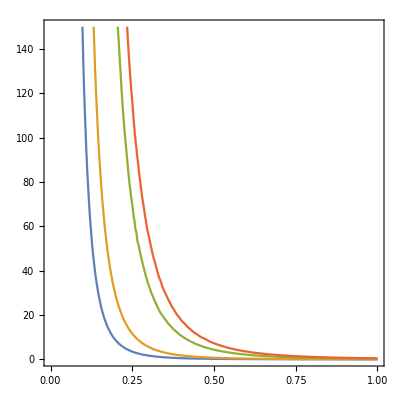

```mathematica
ContourPlot[{(4/7)*(11/4)^(4/3) gh * ξ^4==0.03,(4/7)*(11/4)^(4/3) gh * ξ^4==0.1,(4/7)*(11/4)^(4/3) gh * ξ^4==0.6,(4/7)*(11/4)^(4/3) gh * ξ^4==1},{ξ, 0, 1},{gh,0,150}]
```

```mathematica
ΔNeffweird = Sum[(4/7)(11/4)^(4/3)*gh*(0.08/((i^2)^(1/4)))^4,{i,100}] (*starting value taken for 100 GeV reheaton*)
```

0.000147439 gh

Worst case scenario is where all exotic sector pions are still thermal and relativistic, leptons are still thermal and relativistic, and photons and massless Ws are thermal.

```mathematica
ghwc = 35 + (7/8)*18 + 6
```

227/4

```mathematica
N[ghwc]
```

56.75

```mathematica
worstCase = ΔNeffweird /. gh -> ghwc
```

0.00836716

## Columbia plot stuff

## Determination of gravitational wave signatures

### Energy Density

Here I’ll use h^2 Ω_GW for the current energy density in gravitational waves as this allows for quick comparisons to Pedro’s paper. T_* must be in GeV.

```mathematica
OmegaGW[gs_,OmegaGWs_]:=1.77*10^(-5)(80/gs)^(1/3)*OmegaGWs;
FbPeak[gs_,beta_,Hs_,Ts_]:= 3.33*10^(-8)(gs/80)^(1/6)(Ts/1)(beta/Hs);
FmhdPeak[gs_,beta_,Hs_,Ts_]:= 10FbPeak[gs,beta,Hs,Ts]
```

```mathematica
OmegaGW[80,.0164]
FbPeak[80,1,1,.0164]
FmhdPeak[80,1,1,.0164]
```

2.9028×10^-7

5.4612×10^-10

5.4612×10^-9